```mathematica
(*Question 2*)
(*General Form*)
g =QuantityMagnitude[UnitConvert[Quantity[1,"StandardAccelerationOfGravity"]]];
Distance[x0_,y0_,xv0_,yv0_]:= DSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={0,-g,x0,y0,xv0,yv0},{x[t],y[t]},t]
NDistance[x0_,y0_,xv0_,yv0_]:= NDSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={0,-g,x0,y0,xv0,yv0},{x[t],y[t]},{t,0,1000}]
```

```mathematica
(*Plots for Values of θ*)
```

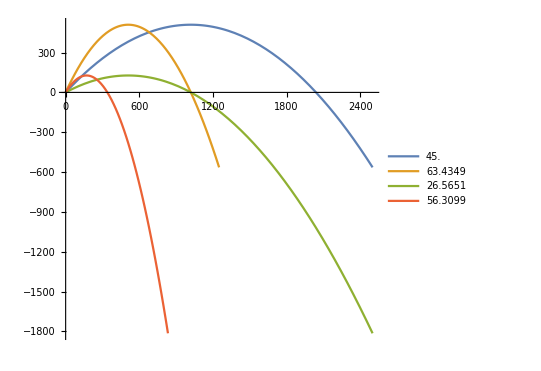

```mathematica
n=100;
Dist1 =Evaluate[{x[t],y[t]}/.NDistance[0,0,n,n]];
Dist2 =Evaluate[{x[t],y[t]}/.NDistance[0,0,n/2,n]];
Dist3 = Evaluate[{x[t],y[t]}/.NDistance[0,0,n,n/2]];
Dist4 = Evaluate[{x[t],y[t]}/.NDistance[0,0,n/3,n/2]];
ParametricPlot[{Dist1,Dist2,Dist3,Dist4},{t,0,25},PlotLegends->{N[ArcTan[n/n]/°],N[ArcTan[n/(n/2)]/°],N[ArcTan[(n/2)/n]/°],N[ArcTan[(n/2)/(n/3)]/°]}]
```

```mathematica
(*Rewritten to just take inputs for V0 and θ*)
```

```mathematica
DistanceTheta[v0_,θ_]:=DSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={0,-QuantityMagnitude[UnitConvert[Quantity[1,"StandardAccelerationOfGravity"]]],0,0,v0*Cos[θ Degree],v0*Sin[θ Degree]},{x[t],y[t]},t]
NDistanceTheta[v0_,θ_]:=NDSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={0,-QuantityMagnitude[UnitConvert[Quantity[1,"StandardAccelerationOfGravity"]]],0,0,v0*Cos[θ Degree],v0*Sin[θ Degree]},{x[t],y[t]},{t,0,1000}]
```

```mathematica
DistTh1 =Evaluate[{x[t],y[t]}/.NDistanceTheta[100,45]];
DistTh2 =Evaluate[{x[t],y[t]}/.NDistanceTheta[100,30]];
DistTh3 =Evaluate[{x[t],y[t]}/.NDistanceTheta[100,60]];
DistTh4 =Evaluate[{x[t],y[t]}/.NDistanceTheta[100,90]];
```

```mathematica
ParametricPlot[{DistTh1,DistTh2,DistTh3,DistTh4},{t,0,20},PlotLegends->{45,30,60,90}]
```

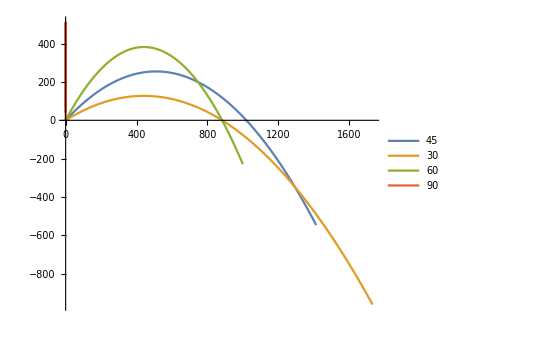

```mathematica
(*You can manipulate θ and see its effect*)
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.NDistanceTheta[100,θ]],{t,0,20},PlotRange->All],{θ,0,90}]
```

```mathematica
(*Question 3*)
```

```mathematica
ρ = QuantityMagnitude[StandardAtmosphereData[Quantity[0,"Feet"],"Density"]]; (*kg/m^3*)
r = 0.05 (*Meters*);
m = 0.5 (*Kilograms*);
A = r^2/2;
DistanceThetaDrag[v0_,θ_]:=DSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={(Abs[-ρ A v0]/m)(x'[t]/v0),-g-(Abs[-ρ A v0]/m)(y'[t]/v0),0,0,v0*Cos[θ Degree],v0*Sin[θ Degree]},{x[t],y[t]},t]
NDistanceThetaDrag[v0_?NumericQ,θ_?NumericQ]:=NDSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={(Abs[-ρ A v0]/m)(x'[t]/v0),-g-(Abs[-ρ A v0]/m)(y'[t]/v0),0,0,v0*Cos[θ Degree],v0*Sin[θ Degree]},{x[t],y[t]},{t,0,1000}]
```

```mathematica
(*MAnitpulate Plot with Drag*)
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.NDistanceThetaDrag[100,θ]],{t,0,20},PlotRange->All],{θ,0,90}]
```

```mathematica
(*Without Drag*)
```

```mathematica
Time[v0_,θ_]:=t/.FindRoot[y[t]/.NDistanceTheta[v0,θ],{t,1000}];
xmax [v0_,θ_]:= (x[t]/.NDistanceTheta[v0,θ]/.t->Time[v0,θ])[[1]]
DistanceFind = xmax[100,45];
```

```mathematica
(*With Drag*)
```

```mathematica
(*We shouldn't have a lower velocity in the drag case be able to go as far as the one we started with ignoring drag*)
```

```mathematica
TimeDrag[v0_?NumericQ,θ_?NumericQ]:= t/.FindRoot[y[t]/.NDistanceThetaDrag[v0,θ],{t,1000}]
xmaxDrag[v0_?NumericQ,θ_?NumericQ]:= (x[t]/.NDistanceThetaDrag[v0,θ]/.t->TimeDrag[v0,θ])[[1]]
VelocityFinder[θ_?NumericQ,tolerance_?NumericQ]:=Module[{v0},
v0=0.0001;
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>250,v0;v0=v0+10];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>100,v0;v0=v0+3];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>10,v0;v0=v0+1];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>tolerance,v0;v0=v0+tolerance/10];
v0
]
ThetaFinderHigh[v0_?NumericQ,tolerance_]:=Module[{θ},
θ  = 90;
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>20 &&θ>0,θ; θ=θ-1];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>tolerance &&θ>0,θ; θ=θ-(tolerance/10)];
θ
]
ThetaFinderLow[v0_?NumericQ,tolerance_]:=Module[{θ},
θ  = 0;
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>20 &&θ < 90,θ; θ=θ+1];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>tolerance &&θ<90,θ; θ=θ+(tolerance/10)];
θ
]
```

```mathematica
(*The Two θs for a initial velocity higher than the Drag-free case, should be complimentary, θ1+θ2=90*)
```

```mathematica
ThetaFinderHigh[110,0.001]
```

62.9638

```mathematica
ThetaFinderLow[110,0.001]
```

27.4312

```mathematica
VelocityFinder[40,0.001]
```

100.096

```mathematica
DistTh1Drag =Evaluate[{x[t],y[t]}/.NDistanceTheta[110,62.9637999999988]];
DistTh2Drag =Evaluate[{x[t],y[t]}/.NDistanceTheta[110,27.431199999998995]];
DistTh3Drag = Evaluate[{x[t],y[t]}/.NDistanceTheta[100.09570000000318,50]];
```

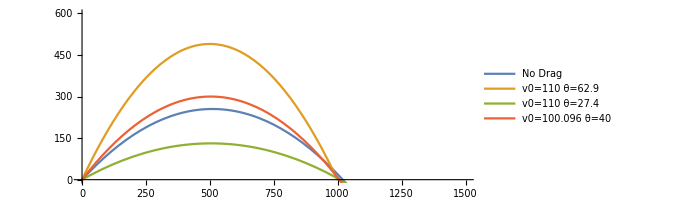

```mathematica
ParametricPlot[{DistTh1,DistTh1Drag,DistTh2Drag,DistTh3Drag},{t,0,20},PlotLegends->{"No Drag","v0=110 θ=62.9","v0=110 θ=27.4","v0=100.096 θ=40"},PlotRange->{{0,1500},{0,600}}]
```